```mathematica
(* This cell contains uninteresting generic setup stuff to prepare for execution of the programs *)

ClearAll["Global`*"];

(* If running from Notebook front end, set directory to Notebook's directory *)
If[Length[$FrontEnd] > 0, NBDir = SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
If[Length[$FrontEnd] == 0,SetDirectory["/Volumes/Data/Work/BufferStock/Endo/Latest/Code/Mathematica/Results/Endo"]];

HomeDir = Directory[];
CodeDir = HomeDir<>"/../../CoreCode";
CDToHomeDir := SetDirectory[HomeDir];
CDToCodeDir := SetDirectory[HomeDir<>"/../../CoreCode"];
CDToCodeDir;

<<SetupModelSolutionRoutines.m;
<<SetParamsToBaselineVals.m;
CDToHomeDir;
```

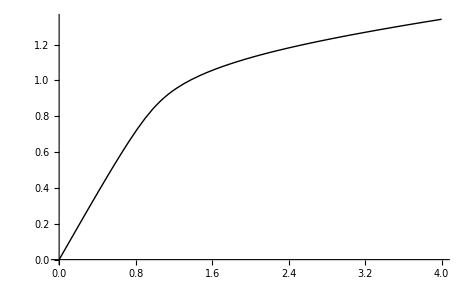

```mathematica
SetParamsBaseline;
SetupGrids;
SetupShocks;
ConstructLastPeriod;
SolveInfHorizToToleranceAtTarget[mTargetDiffAtSuccessiveIterations=0.001];
Print[𝒸WithΓ103Plot = Plot[𝒸[mPlot],{mPlot,0,4}]];
```

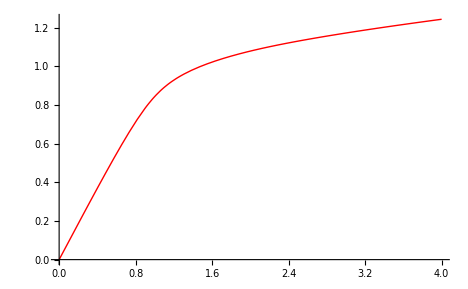

```mathematica
(* Solve with slower income growth => greater patience *)
SetParamsBaseline;
Γ=1.02;
ConstructLastPeriodToConsumeEverything;
SetupGrids;
SetupShocks;
SolveInfHorizToToleranceAtTarget[mTargetDiffAtSuccessiveIterations=0.001];
Print[𝒸WithΓ102Plot = Plot[𝒸[mPlot],{mPlot,0,4},PlotStyle->Red]];
```

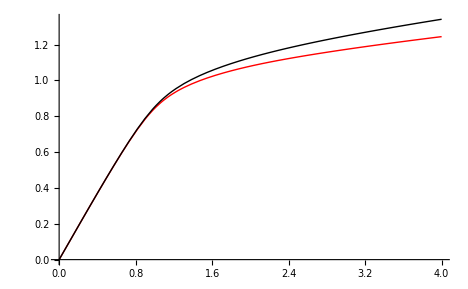

```mathematica
Show[𝒸WithΓ102Plot,𝒸WithΓ103Plot,PlotRange->All]
```